```mathematica
f[x_]:=x^3
```

```mathematica
do[f[(i/j)*k],{i,1,10},{j,1,5},{k,1,2}]
```

do[(i^3 k^3)/j^3,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
do[f[(i)],{i,1,10},{j,1,5},{k,1,2}]
```

do[i^3,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
do[Print[f[(i)]],{i,1,10},{j,1,5},{k,1,2}]
```

i^3

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
i
```

i

```mathematica
f[i]
```

i^3

```mathematica
do[Print[f[2]],{i,1,10},{j,1,5},{k,1,2}]
```

8

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
do[Print[f[2]*i],{i,1,10},{j,1,5},{k,1,2}]
```

8 i

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
do[Print[i],{i,1,10},{j,1,5},{k,1,2}]
```

i

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
Do[Print[f[(i)]],{i,1,10},{j,1,5},{k,1,2}]
```

1

1

1

«7 more identical outputs»

8

8

8

«7 more identical outputs»

27

27

27

«7 more identical outputs»

64

64

64

«7 more identical outputs»

125

125

125

«7 more identical outputs»

216

216

216

«7 more identical outputs»

343

343

343

«7 more identical outputs»

512

512

512

«7 more identical outputs»

729

729

729

«7 more identical outputs»

1000

1000

1000

«7 more identical outputs»

```mathematica
do[Print[f[(i)]],{i,1,10},{j,1,5},{k,1,2}]
```

i^3

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
Do[Print[f[(i)]],{i,1,10},{j,1,5},{k,1,2}]
```

1

1

1

«7 more identical outputs»

8

8

8

«7 more identical outputs»

27

27

27

«7 more identical outputs»

64

64

64

«7 more identical outputs»

125

125

125

«7 more identical outputs»

216

216

216

«7 more identical outputs»

343

343

343

«7 more identical outputs»

512

512

512

«7 more identical outputs»

729

729

729

«7 more identical outputs»

1000

1000

1000

«7 more identical outputs»

```mathematica
1
```

1

```mathematica
PrimeQ[1]
```

False

```mathematica
7
```

7

```mathematica
N[First/@PowersRepresentations[PartitionsQ[7],2,2]]
```

{1.}

```mathematica
k
```

k

```mathematica
print
```

print

```mathematica
Print[k]
```

k

```mathematica
(x+1)^3
```

(1+x)^3

```mathematica
Expand[(x+1)^3]
```

1+3 x+3 x^2+x^3

```mathematica
x=x+1
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[1+x]

```mathematica
x=1
```

1

```mathematica
x*y=2
```

Set::write: Tag Times in 1\ y is Protected.

2

```mathematica
y
```

y

```mathematica
y/1
```

y

```mathematica
y/2
```

y/2

```mathematica
Variables[y]
```

{y}

```mathematica
y
```

y

```mathematica
x=y*2
```

2 y

```mathematica
x
```

2 y

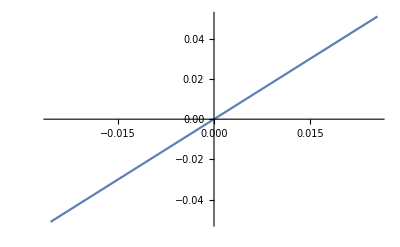

```mathematica
Plot[2 y,{y,-0.025500000000000002,0.025500000000000002}]
```

```mathematica
x=1=2y
```

Set::setraw: Cannot assign to raw object 1.

2 y

```mathematica
x==2y
```

True

```mathematica
x==1
```

2 y==1

```mathematica
Solve[x==1,{y}]
```

{{y→1/2}}

WolframAlphaQueryNoResults

WolframAlphaQueryParseResults

Stephen Wolfram

WolframAlphaQueryParseResults

Wolfram Research

WolframAlphaQueryNoResults

WolframAlphaQueryNoResults

WolframAlphaQueryResults

-Graphics-

WolframAlphaQueryParseResults

34.0147

WolframAlphaQueryParseResults

15.9994

WolframAlphaQueryParseResults

2.01588

WolframAlphaQueryParseResults

34.0147

WolframAlphaQueryResults

31.9988

```mathematica
f(x,y):=x*y
```

Syntax::sntxf: "(" cannot be followed by "x, y)""".

```mathematica
f[x_,y_]:=x+y
```

```mathematica
f[1,2]
```

3

```mathematica
Table[f[i,j],{i,2},{j,2}]
```

{{2,3},{3,4}}

```mathematica
MatrixForm[Table[f[i,j],{i,2},{j,2}]]
```

(2 | 3
3 | 4)

```mathematica
PrimeQ[PrimePi[Total[Sort[Reverse[First/@Table[f[i,j],{i,2,3},{j,2,3}]]]]]]
```

False

```mathematica
Needs["WSMLink`"]
```

```mathematica
field[i_,j_]:=WSMSimulate["EFieldRunner",WSMParameterValues->{"tparticle1.x0"->{i},"tparticle1.y0"->{j}}]
```

```mathematica
fie=field[4,0]
```

WSMSimulate::bld: Failed to build model "EFieldLine.EFieldRunner".

WSMSimulate::bldl: "[/Users/Shanku/Documents/GitHub/EFieldLine/EFieldLine/Components/TParticle.mo:21:3-21:11:writable] Error: Type mismatch in equation tparticle1.E.Px=tparticle1.x of type Real(quantity = \\\"Length\\\", unit = \\\"m\\\")=Boolean."

WSMSimulate::bldl: "Error: Error occurred while flattening model EFieldLine.EFieldRunner"

$Failed

```mathematica
fie=field[4,0]
```

WSMSimulate::bld: Failed to build model "EFieldLine.EFieldRunner".

WSMSimulate::bldl: "[<interactive>:8:3-8:188:writable] Warning: Connecting two signal sources while connecting tparticle1.y to yField."

WSMSimulate::bldl: "[<interactive>:9:3-9:194:writable] Warning: Connecting two signal sources while connecting tparticle1.x to xField."

WSMSimulate::bldl: "Error: Simulation model is not globally balanced, having 23 variables and 25 equations."

General::stop: Further output of WSMSimulate :: bldl will be suppressed during this calculation.

$Failed

```mathematica
fie=field[4,0]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 32.865"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulationData[…]

```mathematica
ParametricPlot[{xField[x],yField[x]},{x,0,32.865}]
```

-Graphics-

```mathematica
xField=fie["tparticle1.x"]
```

InterpolatingFunction[{{0., 32.865}}, <>]

```mathematica
yField=fie["tparticle1.y"]
```

InterpolatingFunction[{{0., 32.865}}, <>]

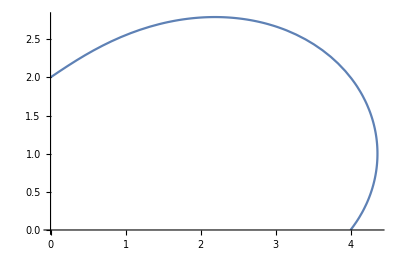

```mathematica
ParametricPlot[{xField[x],yField[x]},{x,0,32.865}]
```

```mathematica
fie2=field[4,1]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 25.1148"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulationData[…]

```mathematica
xField2=fie["tparticle1.x"]
```

InterpolatingFunction[{{0., 32.865}}, <>]

```mathematica
xField2=fie2["tparticle1.x"]
```

InterpolatingFunction[{{0., 25.1148}}, <>]

```mathematica
yField2=fie2["tparticle1.y"]
```

InterpolatingFunction[{{0., 25.1148}}, <>]

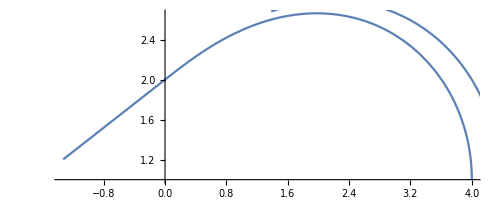

```mathematica
Show[ParametricPlot[{xField2[x],yField2[x]},{x,0,32.865}],ParametricPlot[{xField[x],yField[x]},{x,0,25.1148}]]
```

```mathematica
Show[%98,ImageSize->Tiny]
```

-Graphics-

```mathematica
pfie=ParametricPlot[{xField[x],yField[x]},{x,0,32.865}]
```

-Graphics-

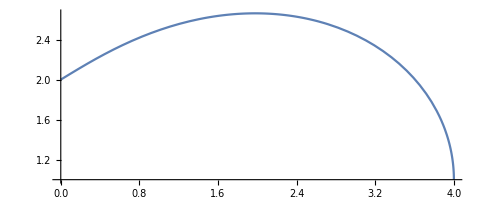

```mathematica
pfie2=ParametricPlot[{xField2[x],yField2[x]},{x,0,25.1148}]
```

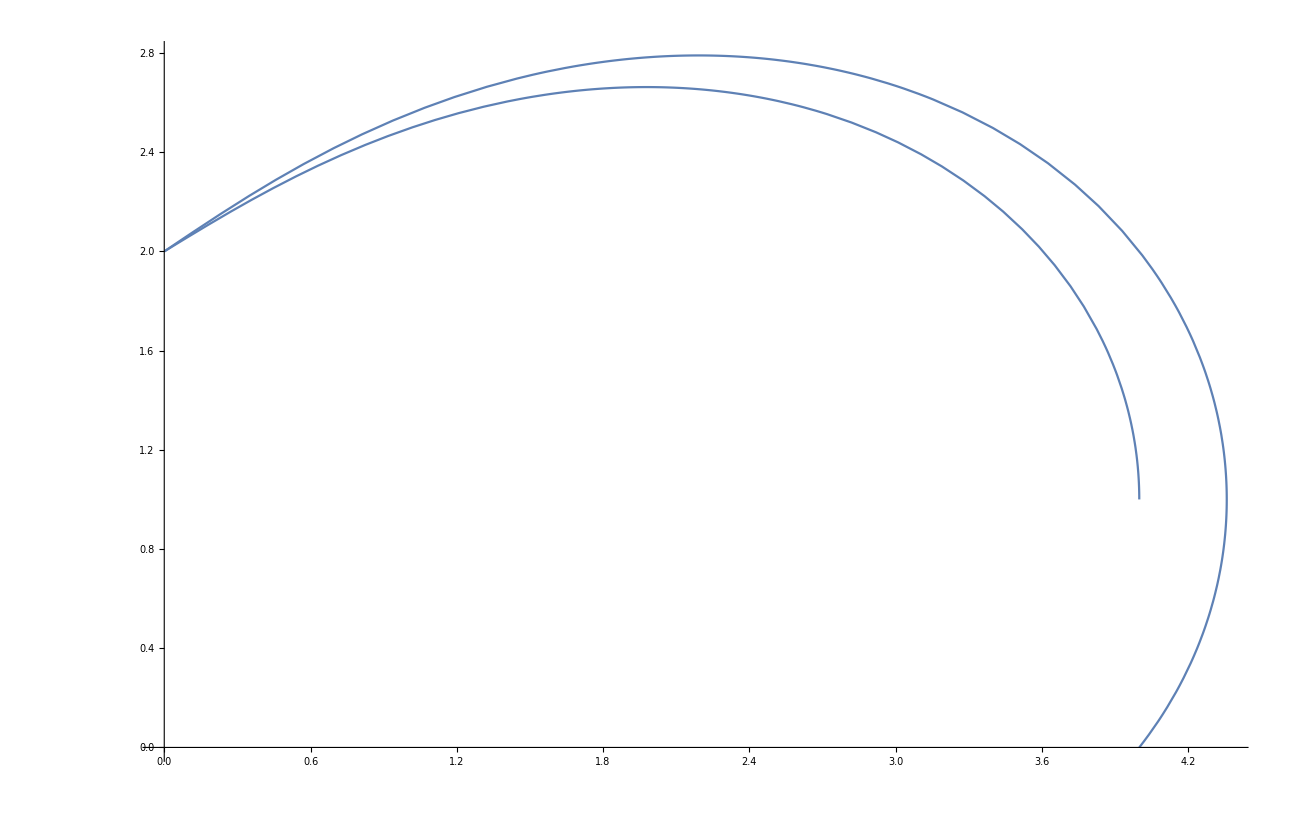

```mathematica
Show[pfie,pfie2]
```

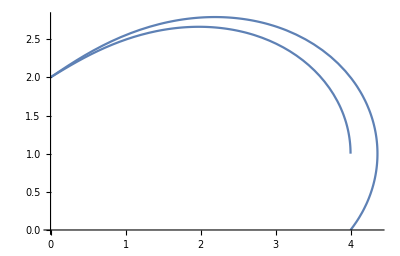

```mathematica
Show[%102,ImageSize->Full]
```

```mathematica
a[1,1]=1
```

1

```mathematica
a[1,2]=2
```

2

```mathematica
a
```

a

```mathematica
Information[a]
```

Global`a

a[1,1]=1
 
a[1,2]=2

```mathematica
a[1,:]
```

Syntax::tsntxi: "a[1, :]" is incomplete; more input is needed.""

```mathematica
xField
```

InterpolatingFunction[{{0., 32.865}}, <>]

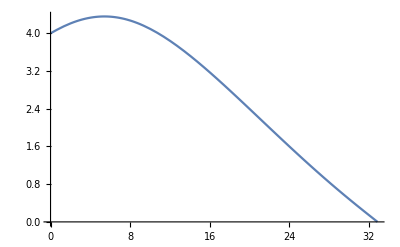

```mathematica
Plot[%108[x],{x,0.,32.86502620577364}]
```

```mathematica
Evaluate[xField]
```

InterpolatingFunction[{{0., 32.865}}, <>]

```mathematica
%110[1.23]
```

4.13903